```mathematica
filename = FileNameJoin[{root = "C:\\Users\\Alex\\Desktop\\SieveProj\\Data", file = "Primelist.xml"}];
If[! DirectoryQ[root], 
  Print[Style["Directory '" <> root <> "' does not exist!", {Red, Bold, Large}]]; Quit[]];
If[! FileExistsQ[filename], 
  Print[Style["File '" <> filename <> "' does not exist!", {Red, Bold, Large}]]; Quit[]];
primeList=Import[filename];   (* xml file doesnt not need "Data" tag to import *)

(*-------------------*)
Needs["PlotLegends`"]
(*----------------------*)
virginScopeArray={};
startLength=Length[primeList];

(* ---------------------------------------------- *)
populateScopeArray[initvar1_]:=(
Catch[
Catch[
Catch[
	returnVal=False;
	virginPrimeList={};
		generateNewPrimes[primeList,initvar1];
	If[startLength<Length[primeList],Throw[True,b]]

	Throw[False,a]
,a
]
Print[initvar1,"was not enough"];
populateScopeArray[initvar1+1];
Throw[False,c]
,b
]
Print[initvar1,"was enough",Length[primeList]-startLength,"primes found"];
,c
]
);
(*------------------------------------------- *)
(*populateScopeArray[1]*)


horoScope1Array=Drop[Drop[primeList,1]-Drop[primeList,-1],1];(* the distance between 2 and 3 is being ignored. *)
virginScopeArray=Drop[primeList,2]-Drop[primeList,-2];
horoScope2Array=Drop[Drop[virginScopeArray,-2],3];
virginScopeArray=Drop[primeList,3]-Drop[primeList,-3];
horoScope3Array=Drop[Drop[virginScopeArray,-2],3];
virginScopeArray=Drop[primeList,4]-Drop[primeList,-4];
horoScope4Array=Drop[Drop[virginScopeArray,-2],3];
```

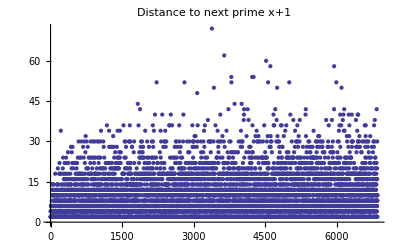

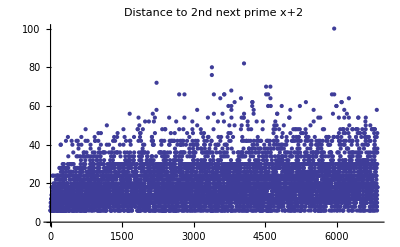

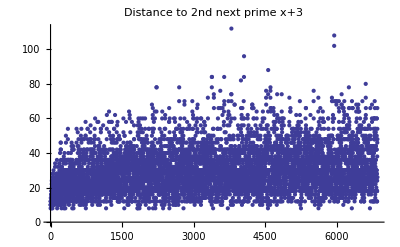

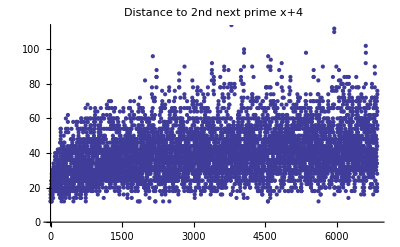

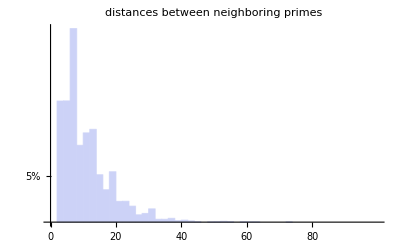
-Graphics--Graphics- | 10.0668 Mean
-Graphics- | 8 Median
-Graphics- | 2 Min
-Graphics- | 72 MAX

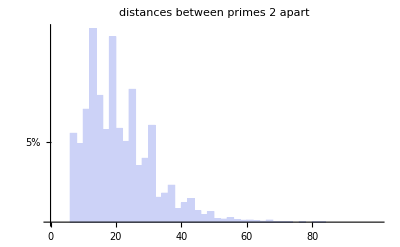
-Graphics--Graphics- | 20.1419 Mean
-Graphics- | 18 Median
-Graphics- | 6 Min
-Graphics- | 100 MAX

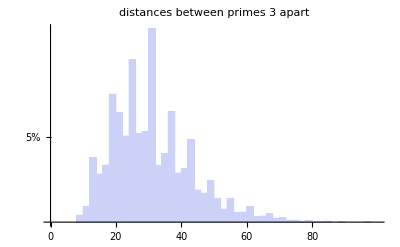
-Graphics--Graphics- | 30.2146 Mean
-Graphics- | 28 Median
-Graphics- | 8 Min
-Graphics- | 112 MAX

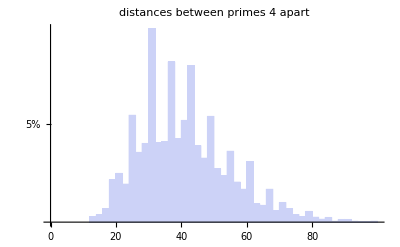
-Graphics--Graphics- | 40.2885 Mean
-Graphics- | 38 Median
-Graphics- | 12 Min
-Graphics- | 126 MAX

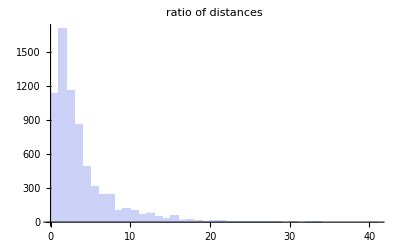
-Graphics--Graphics- | 3.51426 Mean
-Graphics- | (7 Median)/3
-Graphics- | Min/10
-Graphics- | 40 MAX

FittedModel[-2095.45+10.2598 x]

-962.47+8.86702 x+0.000200771 x^2

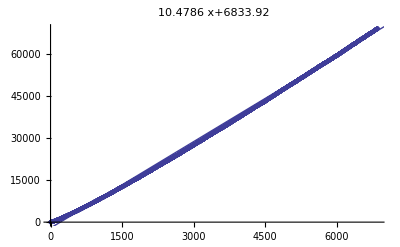

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2095.45 | 17.0115 | -123.179 | 2.7664245437×10^-1735
x | 10.2598 | 0.00432684 | 2371.2 | 1.777603187×10^-9932

```mathematica
bins={Range[0,100,2]};
(*
Histogram[Take[horoScope1Array,1000],PlotLabel->Style[{"0-1k:",N[Mean[Take[horoScope1Array,1000]]]},FontSize->18]]
Histogram[Take[horoScope1Array,{1000,2000}],PlotLabel->Style[{"1-2k:",N[Mean[Take[horoScope1Array,2000]]]},FontSize->18]]
Histogram[Take[horoScope1Array,{2000,3000}],PlotLabel->Style[{"2-3k:",N[Mean[Take[horoScope1Array,3000]]]},FontSize->18]]
Histogram[Take[horoScope1Array,-1000],PlotLabel->Style[{"mean before last 1000:",N[Mean[Take[horoScope1Array,-1000]]]},FontSize->18]]

Histogram[
	{Take[horoScope1Array,1000],Take[horoScope1Array,{1000,2000}],Take[horoScope1Array,{2000,3000}]},
	{1},(* bin width *)
	ChartLayout->"Stacked",
	ChartStyle->46,
	PlotLabel->Style["superimposed groups","Title",14],
	ChartLegends->{"1-1000","1k-2k","2k-3k"},
	AxesLabel->{"prime index","seperation from last prime"}
	]

*)
ListPlot[horoScope1Array,PlotRange->{0,72},PlotLabel->Style["Distance to next prime x+1",FontSize->18]]
ListPlot[horoScope2Array,PlotRange->{0,100},PlotLabel->Style["Distance to 2nd next prime x+2",FontSize->18]]
ListPlot[horoScope3Array,PlotRange->{0,112},PlotLabel->Style["Distance to 2nd next prime x+3",FontSize->18]]
ListPlot[horoScope4Array,PlotRange->{0,112},PlotLabel->Style["Distance to 2nd next prime x+4",FontSize->18]]

Histogram[horoScope1Array,bins,"Probability",
Ticks->{First@bins,
		 Table[{.01 i, If[Mod[i , 5] == 0, ToString[i] <> "%", ""]}, {i, 100}]},
PlotLabel->Style["distances between neighboring primes","Title",14],
	ChartLegends->{"Mean"N[Mean[horoScope1Array]],"Median"Median[horoScope1Array],"Min"Min[horoScope1Array],"MAX"Max[horoScope1Array]}]

Histogram[horoScope2Array,bins,"Probability",
Ticks->{First@bins,
		 Table[{.01 i, If[Mod[i , 5] == 0, ToString[i] <> "%", ""]}, {i, 100}]},
PlotLabel->Style["distances between primes 2 apart","Title",14],
	ChartLegends->{"Mean"N[Mean[horoScope2Array]],"Median"Median[horoScope2Array],"Min"Min[horoScope2Array],"MAX"Max[horoScope2Array]}]

Histogram[horoScope3Array,bins,"Probability",
Ticks->{First@bins,
		 Table[{.01 i, If[Mod[i , 5] == 0, ToString[i] <> "%", ""]}, {i, 100}]},
PlotLabel->Style["distances between primes 3 apart","Title",14],
	ChartLegends->{"Mean"N[Mean[horoScope3Array]],"Median"Median[horoScope3Array],"Min"Min[horoScope3Array],"MAX"Max[horoScope3Array]}]

Histogram[horoScope4Array,bins,"Probability",
Ticks->{First@bins,
		 Table[{.01 i, If[Mod[i , 5] == 0, ToString[i] <> "%", ""]}, {i, 100}]},
PlotLabel->Style["distances between primes 4 apart","Title",14],
	ChartLegends->{"Mean"N[Mean[horoScope4Array]],"Median"Median[horoScope4Array],"Min"Min[horoScope4Array],"MAX"Max[horoScope4Array]}]


ratio21Array=horoScope2Array/Drop[horoScope1Array,-5];
Histogram[ratio21Array,{1},PlotLabel->Style["ratio of distances","Title",14],
	ChartLegends->{"Mean"N[Mean[ratio21Array]],"Median"Median[ratio21Array],"Min"Min[ratio21Array],"MAX"Max[ratio21Array]}]


primeListPlot=ListPlot[primeList,PlotLabel->Style[Fit[Drop[primeList,1000],{1,x},x],FontSize->18]];

model=LinearModelFit[Drop[primeList,50],x,x]
primeFitPlot=Plot[model["BestFit"],{x,0,7000}];
Show[primeListPlot,primeFitPlot]

model["ParameterTable"]
```

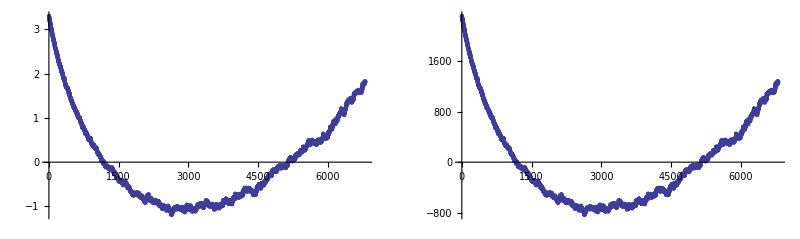

```mathematica
{sr,fr}=model[{"StandardizedResiduals", "FitResiduals"}];{{ListPlot[sr], ListPlot[fr]}}//GraphicsGrid
```

```mathematica
(*
commonDistanceValues={2};
howmanyareder=1;
Do[
	Catch[
	Do[
		If[Mod[commonDistanceValues[[k]],horoScope1Array[[i]]]==0, Throw[False,a];]
		,{k,1,5}
	]
		commonDistanceValues=Append[commonDistanceValues,horoScope1Array[[i]]];
	,a]
	,{i,1,Length[horoScope1Array]}
]
(*
tempHoro=horoScope1Array/2;
nonTwos={};
Catch[
	Do[
	Catch[
		If[tempHoro[[i]]==1,tempHoro=Delete[tempHoro,i];Throw[Null,b];]
		If[Mod[tempHoro[[i]],2]>0,nonTwos=Append[nonTwos,tempHoro[[i]]];tempHoro=Delete[tempHoro,i];Throw[Null,b]]
	,b]
		,{i,1,Length[tempHoro]}
	]
,a]
nonTwos
tempHoro
*)
```

Part::partw: Part 2 of {2} does not exist.

Part::partw: Part 3 of {2} does not exist.

Part::partw: Part 4 of {2} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Set::write: Tag Times in Null\ {2} is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.